```mathematica
pp1[n_,s_]:=Sum[j^(-1/2+s I)+j^(-1/2-s I),{j,1,n}]-Integrate[j^(-1/2+s I)+j^(-1/2-s I),{j,0,n}]
pp2[n_,s_]:=Sum[j^(-1/2+s I)+j^(-1/2-s I),{j,1,n}]-((2 n^(1/2-ⅈ s))/(1+4 s^2)+(2 n^(1/2+ⅈ s))/(1+4 s^2)+(4 ⅈ n^(1/2-ⅈ s) s)/(1+4 s^2)-(4 ⅈ n^(1/2+ⅈ s) s)/(1+4 s^2))
pp3[n_,s_]:=Sum[j^(-1/2+s I)+j^(-1/2-s I),{j,1,n}]-(4/(1+4s^2))((1/2) n^(1/2-ⅈ s)+(1/2) n^(1/2+ⅈ s)+ ⅈ n^(1/2-ⅈ s) s- ⅈ n^(1/2+ⅈ s) s)
pp4[n_,s_]:=Sum[j^(-1/2)(E^(s Log[j] I)+E^(-s Log[j] I)),{j,1,n}]-(4n^(1/2)/(1+4s^2))((1/2) n^(-ⅈ s)+(1/2) n^(ⅈ s)+ ⅈ n^(-ⅈ s) s- ⅈ n^(ⅈ s) s)
pp5[n_,s_]:=2Sum[j^(-1/2)Cos[s Log[j]],{j,1,n}]-(4n^(1/2)/(1+4s^2))((1/2) n^(-ⅈ s)+(1/2) n^(ⅈ s)+ ⅈ n^(-ⅈ s) s- ⅈ n^(ⅈ s) s)
pp6[n_,s_]:=2Sum[j^(-1/2)Cos[s Log[j]],{j,1,n}]-(4n^(1/2)/(1+4s^2))((1/2) (n^(-ⅈ s)+ n^(ⅈ s))+ (s I)( n^(-ⅈ s) - n^(ⅈ s)))
pp7[n_,s_]:=2Sum[j^(-1/2)Cos[s Log[j]],{j,1,n}]-(4n^(1/2)/(1+4s^2))((1/2) (E^(-ⅈ Log[n] s)+ E^(ⅈ Log[n] s))+ (s I)( E^(-ⅈ Log[n] s) - E^(ⅈ Log[n] s)))
pp8[n_,s_]:=2Sum[j^(-1/2)Cos[s Log[j]],{j,1,n}]-(4n^(1/2)/(1+4s^2))((1/2) (E^(-ⅈ Log[n] s)+ E^(ⅈ Log[n] s))+ 2s Sin[Log[n]s])
pp9[n_,s_]:=Sum[j^(-1/2)Cos[s Log[j]],{j,1,n}]-(2n^(1/2)/(1+4s^2))(2s Sin[Log[n]s]+Cos[Log[n] s])
```

```mathematica
pp9[1000,10.+.2I]
```

1.58287+0.00192283 ⅈ

```mathematica
pp2[1000,10.+.2I]/2
```

1.58287+0.00192283 ⅈ

```mathematica
(Zeta[.5+s]+Zeta[.5-s])/2/.s->(10I+.2)
```

1.54944-0.000866905 ⅈ

```mathematica
Integrate[j^(-1/2+s I)+j^(-1/2-s I),{j,0,n}]
```

ConditionalExpression[(2 n^(1/2-ⅈ s) (1+n^(2 ⅈ s) (1-2 ⅈ s)+2 ⅈ s))/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
Integrate[j^(-1/2-s I),{j,0,n}]
```

ConditionalExpression[(2 ⅈ n^(1/2-ⅈ s))/(ⅈ+2 s),Im[s]>-1/2]

```mathematica
Expand[(2 n^(1/2-ⅈ s) (1+n^(2 ⅈ s) (1-2 ⅈ s)+2 ⅈ s))/(1+4 s^2)]
```

(2 n^(1/2-ⅈ s))/(1+4 s^2)+(2 n^(1/2+ⅈ s))/(1+4 s^2)+(4 ⅈ n^(1/2-ⅈ s) s)/(1+4 s^2)-(4 ⅈ n^(1/2+ⅈ s) s)/(1+4 s^2)

```mathematica
N[E^(s Log[j] I)+E^(-s Log[j] I)/.s->3/.j->2]
```

-0.973989+0. ⅈ

```mathematica
N[2 Cos[s Log[j]]/.s->3/.j->2]
```

-0.973989

```mathematica
N[(s I)( E^(-ⅈ Log[n] s) - E^(ⅈ Log[n] s))/.s->3/.n->2]
```

5.24043+0. ⅈ

```mathematica
N[2s Sin[Log[n]s]/.s->3/.n->2]
```

5.24043

```mathematica
FullSimplify[(Zeta[1/2+s]+Zeta[1/2-s])/2/.s->(-1/2+ZetaZero[1])]
```

0

```mathematica
Sum[j^(-1/2)Cos[s Log[j]],{j,1,n}]-(2n^(1/2)/(1+4s^2))(2s Sin[Log[n]s]+Cos[Log[n] s])
```

-(2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)+∑_(j=1)^n Cos[s Log[j]]/(√j)

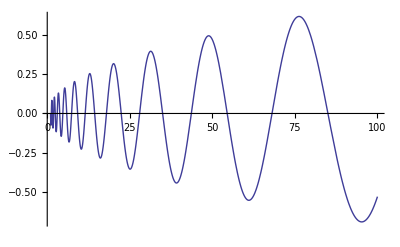

```mathematica
Plot[-(2 √n (Cos[s Log[n]]+2 s Sin[s Log[n]]))/(1+4 s^2)/.s->Im@ZetaZero@1,{n,1,100}]
```

```mathematica
ee1[n_,s_]:=Sum[j^(-1/2+s I)-j^(-1/2-s I),{j,1,n}]-Integrate[j^(-1/2+s I)-j^(-1/2-s I),{j,0,n}]
ee2[n_,s_]:=Sum[j^(-1/2+s I)-j^(-1/2-s I),{j,1,n}]-(-(2 n^(1/2-ⅈ s))/(1+4 s^2)+(2 n^(1/2+ⅈ s))/(1+4 s^2)-(4 ⅈ n^(1/2-ⅈ s) s)/(1+4 s^2)-(4 ⅈ n^(1/2+ⅈ s) s)/(1+4 s^2))
ee3[n_,s_]:=Sum[j^(-1/2)(E^(s Log[j] I)-E^(-s Log[j] I)),{j,1,n}]-(-(2 n^(1/2-ⅈ s))/(1+4 s^2)+(2 n^(1/2+ⅈ s))/(1+4 s^2)-(4 ⅈ n^(1/2-ⅈ s) s)/(1+4 s^2)-(4 ⅈ n^(1/2+ⅈ s) s)/(1+4 s^2))
ee4[n_,s_]:=2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(-(2 n^(1/2-ⅈ s))/(1+4 s^2)+(2 n^(1/2+ⅈ s))/(1+4 s^2)-(4 ⅈ n^(1/2-ⅈ s) s)/(1+4 s^2)-(4 ⅈ n^(1/2+ⅈ s) s)/(1+4 s^2))
ee5[n_,s_]:=2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(2n^(1/2)/(1+4s^2))(- n^(-ⅈ s)+ n^(+ⅈ s)-2 ⅈ n^(-ⅈ s) s-2 ⅈ n^(+ⅈ s) s)
ee6[n_,s_]:=2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(2n^(1/2)/(1+4s^2))((- n^(-ⅈ s)+ n^(+ⅈ s))-2 ⅈ s (n^(-ⅈ s) +n^(+ⅈ s)))
ee7[n_,s_]:=2 I Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(2n^(1/2)/(1+4s^2))(2I Sin[s Log[n]]-2 ⅈ s 2 Cos[s Log[n]])
ee8[n_,s_]:= Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]+(2n^(1/2)/(1+4s^2))( 2s Cos[s Log[n]]-Sin[s Log[n]])
```

```mathematica
ee8[1000,10.+.2I]
```

0.112631+0.101817 ⅈ

```mathematica
ee2[1000,10.+.2I]/(2 I)
```

0.112631+0.101817 ⅈ

```mathematica
(Zeta[.5+s]-Zeta[.5-s])/(2 I)/.s->(10I+.2)
```

-0.113829+0.0723504 ⅈ

```mathematica
Expand@Integrate[j^(-1/2+s I)-j^(-1/2-s I),{j,0,n}]
```

ConditionalExpression[-(2 n^(1/2-ⅈ s))/(1+4 s^2)+(2 n^(1/2+ⅈ s))/(1+4 s^2)-(4 ⅈ n^(1/2-ⅈ s) s)/(1+4 s^2)-(4 ⅈ n^(1/2+ⅈ s) s)/(1+4 s^2),-1/2<Im[s]<1/2]

```mathematica
N[(E^(s Log[j] I)-E^(-s Log[j] I))/.s->3/.j->2]
```

0.+1.74681 ⅈ

```mathematica
N[2I Sin[s Log[j]]/.s->3/.j->2]
```

0.+1.74681 ⅈ

```mathematica
N[(- n^(-ⅈ s)+ n^(+ⅈ s))/.s->3/.n->2]
```

0.+1.74681 ⅈ

```mathematica
N[ (n^(-ⅈ s) +n^(+ⅈ s))/.s->3/.n->2]
```

-0.973989+0. ⅈ

```mathematica
N[2 Cos[s Log[j]]/.s->3/.j->2]
```

-0.973989

```mathematica
pp9[n_,s_]:=Sum[j^(-1/2)Cos[s Log[j]],{j,1,n}]-(2n^(1/2)/(1+4s^2))(Cos[Log[n] s]+2s Sin[Log[n]s])
pp9a[s_]:=(Zeta[1/2-s I]+Zeta[1/2+s I])/2
ee9[n_,s_]:= Sum[j^(-1/2)Sin[s Log[j]],{j,1,n}]-(2n^(1/2)/(1+4s^2))( Sin[s Log[n]]-2s Cos[s Log[n]])
ee9a[s_]:=(Zeta[1/2-s I]-Zeta[1/2+s I])/(2 I)
```

```mathematica
pp9[100000,20+.3I]
```

0.376859-0.287306 ⅈ

```mathematica
pp9a[20+.3I]
```

0.391975-0.30721 ⅈ

```mathematica
ee9[100000,10+.2I]
```

0.120979+0.0688678 ⅈ

```mathematica
ee9a[10+.2I]
```

0.113829+0.0723504 ⅈ

```mathematica
pp9[1000000,N@Im@ZetaZero@1]
```

0.000438863

```mathematica
FullSimplify@pp9a[Im@ZetaZero@1]
```

0

```mathematica
ee9[1000000,N@Im@ZetaZero@1]
```

-121.644

```mathematica
FullSimplify@ee9a[Im@ZetaZero@1]
```

0

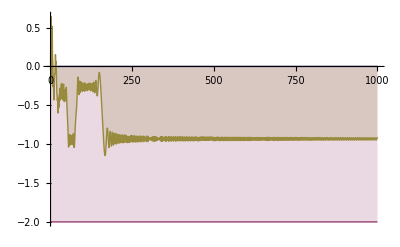

```mathematica
DiscretePlot[{0,-2,ee9[n,1000]},{n,1,1000}]
```

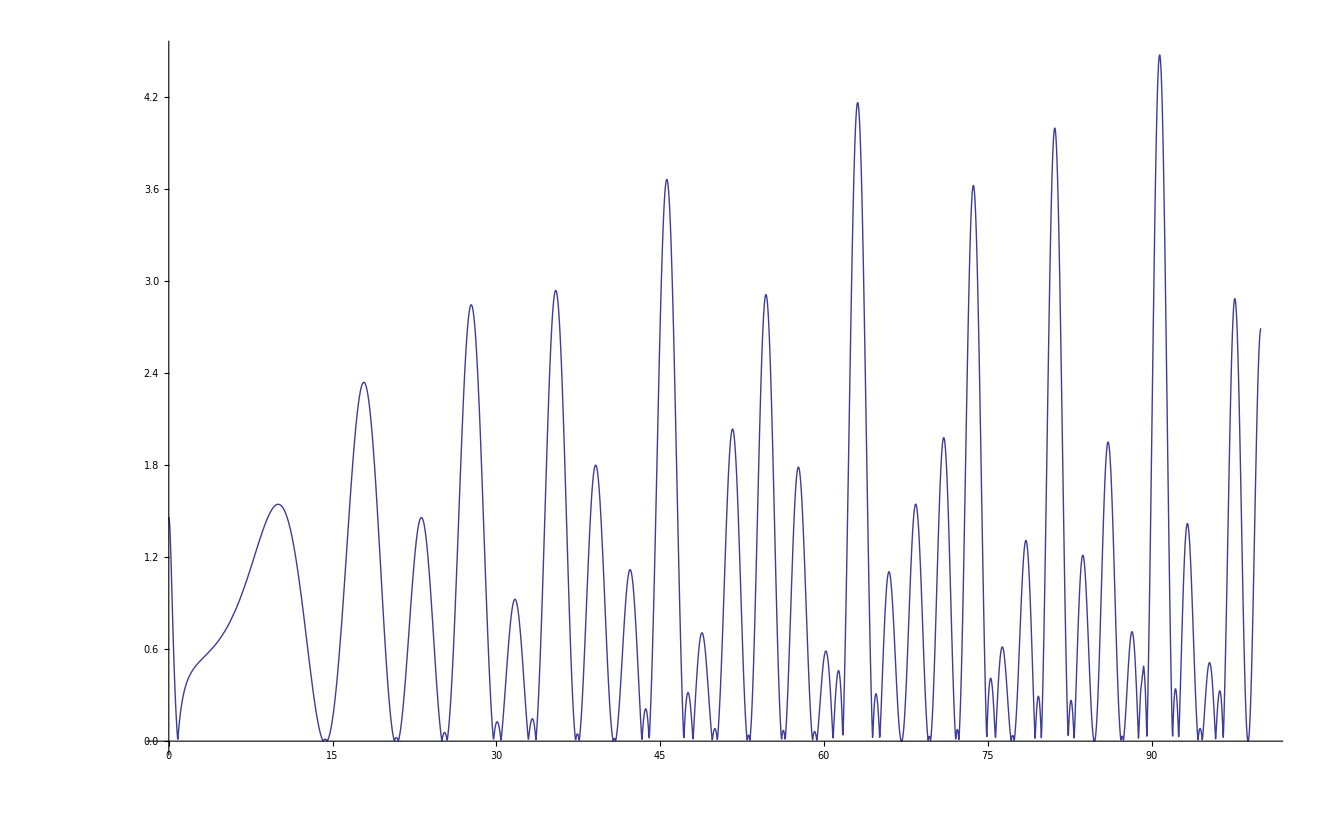

```mathematica
Plot[{Abs@pp9a[n+.01I]},{n,0,100}]
```